## Cosmological Perturbation Theory Package

First, load the package

```mathematica
<<COSPER
```

Get::noopen: Cannot open "COSPER".

$Failed

Brief on-line help is available for all functions:

```mathematica
?IMetric
```

IMetric[g], with g an n.n-matrix (two lower indices),
  returns the inverse metric (two upper indices).

```mathematica
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

## Basic

### Background

First define the coordinate n-vector:

```mathematica
x={t,x1,x2,x3};
```

and then specify the metric as a square n×n matrix:

```mathematica
(met={{-a[t]*a[t],0,0,0},{0,a[t]*a[t],0,0},{0,0,a[t]*a[t],0},{0,0,0,a[t]*a[t]}})//MatrixForm;
```

"IMetric" is the only 1-argument function:

```mathematica
IMetric[met]//MatrixForm;
```

```mathematica
IMetric[met];
```

All other "functions" take two arguments, the metric matrix and then the coordinate vector:

```mathematica
Christoffel[met,x];
```

```mathematica
Riemann[met,x];
```

```mathematica
Ricci[met,x];
```

```mathematica
SCurvature[met,x]
```

(6 a''[t])/a[t]^3

```mathematica
FullSimplify[SCurvature[met,x]];
```

```mathematica
EinsteinTensor[met,x];
```

```mathematica
SqRicci[met,x];
```

```mathematica
SqRiemann[met,x];
```

```mathematica
(EMTensor={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}})//MatrixForm;
```

Friedmann Equation

```mathematica
FriedmannClassic=EinsteinTensor[met,x][[1]][[1]]==κ^2 EMTensor[[1]][[1]];
```

## ΛCDM Model

Hubble function

```mathematica
HL[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=HCurrent √(Omegam0 a^-3+Omegar0 a^-4+OmegaL);
HL1[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=D[HL[a,HCurrent,Omegam0,Omegar0,OmegaL],a];
iHL[a_]:= H0  √(Ωm0 a^-1+ Ωx0)
```

```mathematica
HL[a,H0,Ωm0,Ωr0,Ωx0]
HL[a_]=HL[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a_]=HL1[a,H0,Ωm0,Ωr0,Ωx0]
HM[a_]=HL[a,H0,Ωm0,0,Ωx0]
HM1[a_]=HL1[a,H0,Ωm0,0,Ωx0]
HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]
```

71. √(0.73+0.0000809/a^4+0.27/a^3)

71. √(0.73+0.0000809/a^4+0.27/a^3)

(35.5 (-0.0003236/a^5-0.81/a^4))/(√(0.73+0.0000809/a^4+0.27/a^3))

(35.5 (-0.0003236/a^5-0.81/a^4))/(√(0.73+0.0000809/a^4+0.27/a^3))

71. √(0.73+0.27/a^3)

-28.755/(√(0.73+0.27/a^3) a^4)

-2.14831×10^9

## f(R) Gravity

f(R) signature

```mathematica
Clear[R]
RR[a_,HCurrent_,Constant_,Omegam0_,Omegar0_,mass_]=3 HCurrent^2/c^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/c^2
D[3 HCurrent^2/lightspeed^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant mass^2/lightspeed^2,a];
RR1[a_,HCurrent_,Omegam0_,Omegar0_,mass_]=(3 HCurrent^2 (-(3 Omegam0)/a^4-(4 Omegar0)/a^5))/c^2//Simplify
```

(Constant mass^2)/5000000000+(3 HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/10000000000

-(3 HCurrent^2 (3 a Omegam0+4 Omegar0))/(10000000000 a^5)

n is kinda special. Give the value of it first. Because when doing derivative

```mathematica
(*
Clear[f,fR]
(*fComp[Constant1_,Constant2_,mass_]=ffComp[4,Constant1,Constant2,mass]/.{R->R[a]};*)
f[Constant1_,Constant2_,mass_]=
fR[Constant1_,Constant2_,mass_]=ffR[1,Constant1,Constant2,mass]/.{R->R[a]}
fRR[Constant1_,Constant2_,mass_]=ffRR
*)
```

```mathematica
(*
Clear[f1,fR1,fR2]
f1[Constant1_,Constant2_,mass_]=Simplify[D[f[Constant1,Constant2,mass],a]]
fR1[Constant1_,Constant2_,mass_]=D[fR[Constant1,Constant2,mass],a]//Simplify
fR2[Constant1_,Constant2_,mass_]=D[D[fR[Constant1,Constant2,mass],a],a]
*)
```

Constants and fundamental functions. Units should be determined first.

```mathematica
Clear[Const1,Const2]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
m=H0 √Ωm0;
lp=√(2.47*10^-25);
Const1[nn_]=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^(nn+1)nn/fR0;
Const2[nn_]=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^(nn+1)nn/fR0;
Ω=Ωm0 a^-3+Ωr0 a^-4;
R=3 H0^2 Ωm0 a^-3+12 Ωx0/Ωm0 m^2;
R1=RR1[a,H0,Ωm0,Ωr0,m];
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

-25.1262

First equation: (Omega is the parameter for fraction evolution, so use )

```mathematica
f=-d1 m^2/c^2+d2 m^2/c^2 m^2/R
fR=-d2 m^4 1/R^2
fRR=2d2 m^4 1/R^3 c^2
3 (1+fR)==1/2 (-f+(1-fR) R)+κ^2 (ρm[a]+ρr[a])-3 a fRR H[a]^2 R'[a]
```

-2.45329×10^-7-0.000517184/(44159.2+4083.21/a^3)

(4.65465×10^7)/((44159.2+4083.21/a^3)^2)

-(8.37837×10^18)/((44159.2+4083.21/a^3)^3)

3 (1+(4.65465×10^7)/((44159.2+4083.21/a^3)^2))==1/2 (2.45329×10^-7+0.000517184/(44159.2+4083.21/a^3)+(1-(4.65465×10^7)/((44159.2+4083.21/a^3)^2)) (44159.2+4083.21/a^3))+κ^2 (ρm[a]+ρr[a])+(2.51351×10^19 a H[a]^2 (44159.2+4083.21/a^3)'[a])/((44159.2+4083.21/a^3)^3)

## Background Comparison with LCDM model.

```mathematica
H[a_]=H0√((27 (Ωm0 a^-3)^4+(27*13 Ωx0-3d2)(Ωm0 a^-3)^3+(9*12*15 Ωx0^2-24d2 Ωx0)(Ωm0 a^-3)^2+(21*12^2 Ωx0^3-12*4d2 Ωx0^2)(Ωm0 a^-3)+Ωx0 (12Ωx0)^3+Ωr0 a^-4(27 (Ωm0 a^-3)^3+(12Ωx0)^3+3(3 Ωm0 a^-3)^2 12Ωx0+3(12Ωx0)^2 3Ωm0 a^-3))/(27 (Ωm0 a^-3)^3+27*12 Ωx0 (Ωm0 a^-3)^2+(9*12^2 Ωx0^2-3d2 Ωm0^2-54 d2 Ωm0^2)Ωm0 a^-3+(12 Ωx0)^3-12d2 Ωm0^2 Ωx0))
```

71. √((490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3)/(688.267+0.531441/a^9+17.2423/a^6+214.662/a^3))

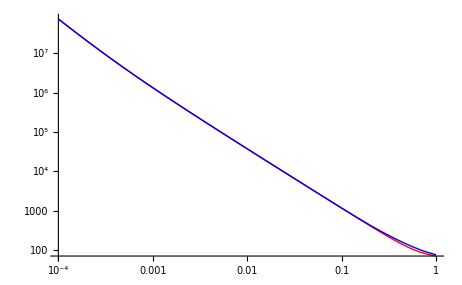

```mathematica
LogLogPlot[{HL[a,H0,Ωm0,Ωr0,Ωx0],H[a]},{a,10^-4,1},PlotStyle->{Red,Blue}]
```

H1[a] is the first derivative of H[a]

```mathematica
H1[a_]=D[H[a],a];
wleff[a_]=-1-2/3 a HL1[a]/HL[a]
wmeff[a_]=-1-2/3 a HM1[a]/HM[a]
weff[a_]=-1-2/3 a H1[a]/H[a]
```

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

-1+0.27/((0.73+0.27/a^3) a^3)

-1-(0.333333 ((-1.72187/a^13-58.7435/a^10-570.155/a^7-(0.0003236 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^5-1473.47/a^4+(0.0000809 (-4.78297/a^10-103.454/a^7-559.417/a^4))/a^4)/(688.267+0.531441/a^9+17.2423/a^6+214.662/a^3)-((-4.78297/a^10-103.454/a^7-643.987/a^4) (490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3))/(688.267+0.531441/a^9+17.2423/a^6+214.662/a^3)^2) (688.267+0.531441/a^9+17.2423/a^6+214.662/a^3) a)/(490.722+0.143489/a^12+6.52705/a^9+95.0258/a^6+(0.0000809 (672.221+0.531441/a^9+17.2423/a^6+186.472/a^3))/a^4+491.156/a^3)

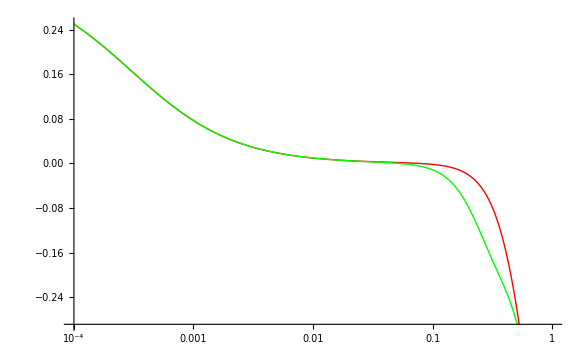

```mathematica
LogLinearPlot[{wleff[a],weff[a]},{a,0.0001,1},PlotStyle->{Red,Green,Blue}]
```

## f(R) Gravity Perturbation

LCDM Model data

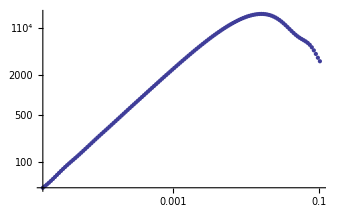

NIntegrate::nlim: temp = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

```mathematica
Clear[GrowthL]
PowerL=Import["cdm_11-27_cut.dat"];
ListLogLogPlot[PowerL]
GrowthL[a_]:= 5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}];
GrowthL1[a_]=D[GrowthL[a],a];
```

Check the divation from LCDM : M

-25.1262

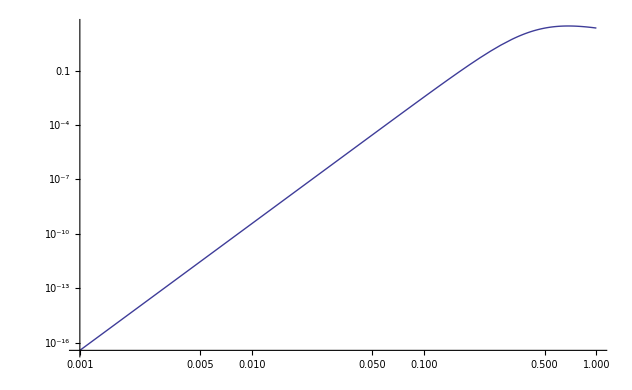

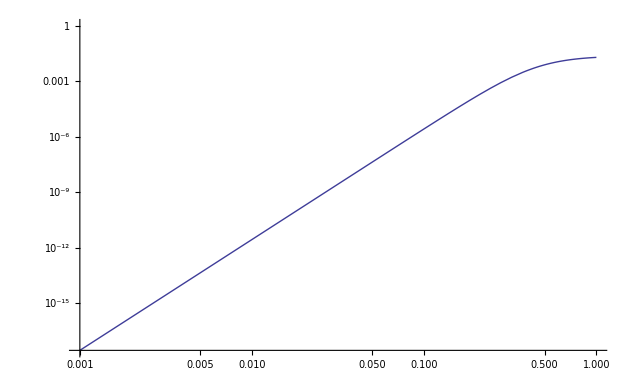

-0.00537272

-Graphics-

-Graphics3D-

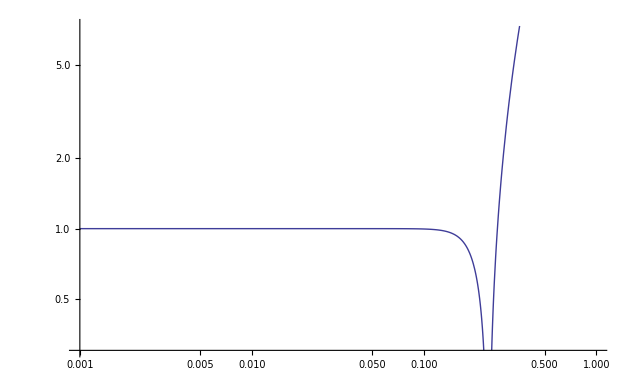

(1+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)-(3.35135×10^19 k^2)/((44159.2+4083.21/a^3)^3 a^2))/((1+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)) (1+(4.65465×10^7)/((44159.2+4083.21/a^3)^2)-(2.51351×10^19 k^2)/((44159.2+4083.21/a^3)^3 a^2)))

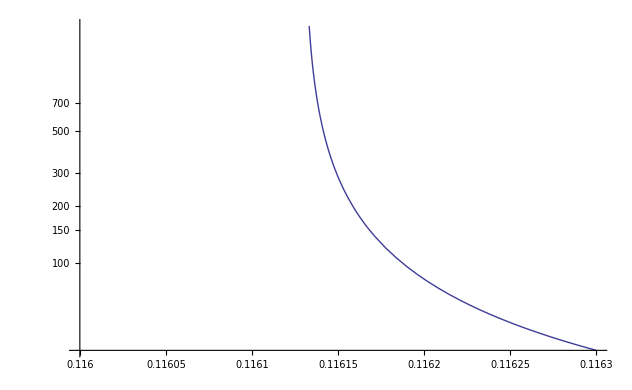

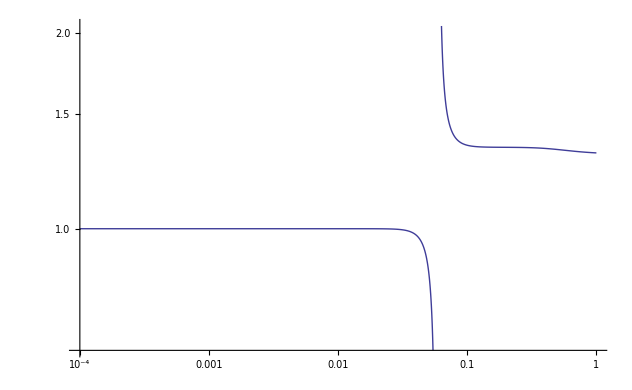

```mathematica
Clear[k]
d2
LogLogPlot[Block[{k=0.01},-6d2 (c^2 k^2)/a^2 m^4/R^3],{a,0.001,1}]
LogLogPlot[fR,{a,0.001,1}]
FindMaxValue[{1/(m^4 1/R^2-3 c^2 k^2/a^3 2 m^4 1/R^3),10^-4<k<0.1,10^-4<a<1},{a,k}]
LogLogPlot[-d2 m^4 1/R^2,{a,0.001,1}]
Plot3D[{Abs[1/((1.852511544900001*^6)/((44159.16000000001+4083.2100000000005/((10^aa)^3))^2)-(1.0003562342460005*^18 (10^kk)^2)/((44159.16000000001+4083.2100000000005/10^(3aa))^3 10^(3 aa)))],1/((1.852511544900001*^6)/((44159.16000000001+4083.2100000000005/((10^aa)^3))^2)-(1.0003562342460005*^18 (10^kk)^2)/((44159.16000000001+4083.2100000000005/10^(3aa))^3 10^(3 aa)))},{kk,-4,-1},{aa,-4,0},AxesLabel->Automatic,PlotRange->{{-4,-1},{-4,0}},ColorFunction->Hue]
LogLogPlot[Abs[Block[{k=0.01},1-d2 m^4 1/R^2+3 (c^2 k^2)/a^2 2d2 m^4 1/R^3]],{a,0.001,1}]
mm[a_,k_]=1/(1+fR)(1-d2 m^4 1/R^2+4(c^2 k^2)/a^2 2 d2 m^4 1/R^3)/(1-d2 m^4 1/R^2+3 (c^2 k^2)/a^2 2d2 m^4 1/R^3)

LogLogPlot[mm[a,0.1],{a,0.116,0.1163}]
LogLogPlot[mm[a,1],{a,0.0001,1}]
```

```mathematica
Clear[a,gg,GrowthfR,solgg]
solgf[a_]=NDSolve[{a^2 gg''[a]+(3+a/H[a] H1[a])a gg'[a]+3/2 1/a^5 H0^2/H[a]^2 Ωm0 (1/(1+fR)(1-d2 m^4 1/R^2+4(c^2 0.1^2)/a^2 2 d2 m^4 1/R^3)/(1-d2 m^4 1/R^2+3 (c^2 0.1^2)/a^2 2d2 m^4 1/R^3))gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-3]==GrowthL'[10^-3]},gg[a],{a,10^-4,1}]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NDSolve::mxst: Maximum number of 10000 steps reached at the point a == 0.000691511.

NDSolve::mxst: Maximum number of 10000 steps reached at the point a == 0.00181109.

{{gg[a]→InterpolatingFunction[{{0.000691511,0.00181109}},<>][a]}}

```mathematica
ListPlot[{Table[{Log[GrowthTable[[i]][[1]]],Log[GrowthTable[[i]][[2]]]},{i,1,365}],Table[{Log[aTable[[i]]],Log[GrowthL[aTable[[i]]]]},{i,1,365}]},Joined->True,PlotStyle->{Black,Red}]
ListPlot[Table[{Log[aTable[[i]]],Log[GrowthL[aTable[[i]]]]},{i,1,365}],Joined->True,PlotStyle->{Black,Red}]
```

Part::partd: Part specification GrowthTable ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification GrowthTable ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::nlim: temp = aTable ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification aTable ⟦ 1 ⟧ is longer than depth of object.

NIntegrate::nlim: temp = aTable ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partd: Part specification aTable ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

## Backup here

```mathematica
Clear[H]
fRFriedmann=3(1+fR)==3 H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3a H[a]^2 fRR R1//FullSimplify
```

1/(a (4083.21+44159.2 a^3))(-0.925442+a (-1.38988×10^14+a^2 (-30.0254+a (-6.01231×10^15+a^2 (-324.72-9.71417×10^16 a-1170.59 a^3-6.9476×10^17 a^4-1.85566×10^18 a^7))))+a^9 (1.23006×10^10+3.07896×10^13 a) H[a]^2)==0

```mathematica
Solve[ H[a]^2==(3 c^2)/(3a fRR R1) H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3(1+fR),H[a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H[a]→-1.15255×10^-50 √(1.66192×10^104-(7.73775×10^111)/((44159.2+4083.21/a^3)^2)+(1.94667×10^96)/(44159.2+4083.21/a^3)+(2.08645×10^100)/(0.0003236+0.81 a)+(1.64949×10^97)/((0.0003236+0.81 a) a^9)+(5.5051×10^100)/((0.0003236+0.81 a) a^8)+(5.35169×10^98)/((0.0003236+0.81 a) a^6)+(1.7861×10^102)/((0.0003236+0.81 a) a^5)+(1.53691×10^103)/a^3-(7.1538×10^110)/((44159.2+4083.21/a^3)^2 a^3)+(5.78775×10^99)/((0.0003236+0.81 a) a^3)+(1.93163×10^103)/((0.0003236+0.81 a) a^2)+(6.96342×10^103 a)/(0.0003236+0.81 a))},{H[a]→1.15255×10^-50 √(1.66192×10^104-(7.73775×10^111)/((44159.2+4083.21/a^3)^2)+(1.94667×10^96)/(44159.2+4083.21/a^3)+(2.08645×10^100)/(0.0003236+0.81 a)+(1.64949×10^97)/((0.0003236+0.81 a) a^9)+(5.5051×10^100)/((0.0003236+0.81 a) a^8)+(5.35169×10^98)/((0.0003236+0.81 a) a^6)+(1.7861×10^102)/((0.0003236+0.81 a) a^5)+(1.53691×10^103)/a^3-(7.1538×10^110)/((44159.2+4083.21/a^3)^2 a^3)+(5.78775×10^99)/((0.0003236+0.81 a) a^3)+(1.93163×10^103)/((0.0003236+0.81 a) a^2)+(6.96342×10^103 a)/(0.0003236+0.81 a))}}

```mathematica
Clear[Sol]
Sol[a_]=NDSolve[{fRFriedmann,H[10^-3]==HL[10^-3,H0,Ωm0,Ωr0,Ωx0],H'[10^-3]==HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]},H[a],{a,10^-4,1}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

Testing Functions

```mathematica
t1=Table[i*10^-4,{i,1,10,0.1}];
t2=Table[i*10^-3,{i,1,10,0.1}];
t3=Table[i*10^-2,{i,1,10,0.1}];
t4=Table[i*10^-1,{i,1,10,0.1}];
t5=Table[i,{i,1,1,0.1}];
aTable=Join[t1,t2,t3,t4,t5];
Length[aTable]
ListPlot[aTable];
```

365

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

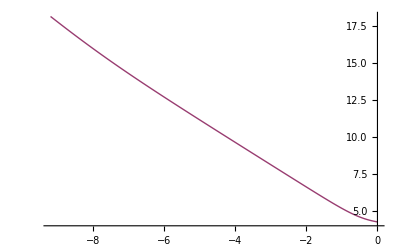

```mathematica
HubbleTable=Table[{Sol[aTable[[i]]][[1]][[1]],HL[aTable[[i]],H0,Ωm0,Ωr0,Ωx0],aTable[[i]]},{i,1,365}];
ListPlot[{Table[{Log[HubbleTable[[i]][[3]]],Log[H[HubbleTable[[i]][[3]]]/.HubbleTable[[i]][[1]]]},{i,1,365}],Table[{Log[HubbleTable[[i]][[3]]],Log[HubbleTable[[i]][[2]]]},{i,1,365}]},Joined->True]
```

ΛCDM as an example

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

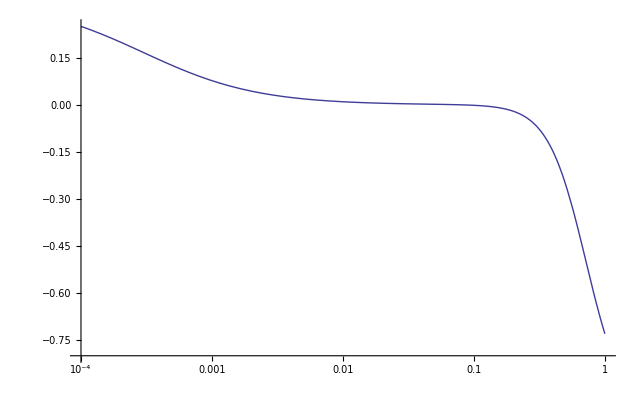

-194729.+3.56799×10^8 a^(1/9)-1.18914×10^9 a^(1/8)+1.55755×10^9 a^(1/7)-1.01651×10^9 a^(1/6)+3.45971×10^8 a^(1/5)-5.86945×10^7 a^(1/4)+4.31573×10^6 a^(1/3)-101465. √a+382.796 a

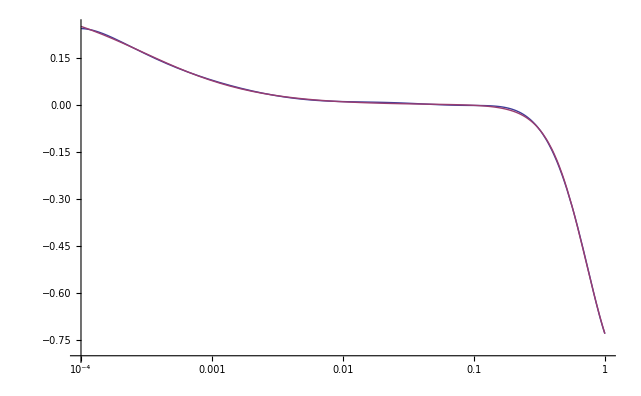

```mathematica
wleff[a_]=-1-2(a HL[a,H0,Ωm0,Ωr0,Ωx0] HL1[a,H0,Ωm0,Ωr0,Ωx0])/(3 HL[a,H0,Ωm0,Ωr0,Ωx0]^2)
LogLinearPlot[wleff[a],{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
wlefff=Table[{aTable[[i]],wleff[aTable[[i]]]},{i,1,365}];
wlefffit[a_]=Fit[wlefff,{1,a,a^(1/2),a^(1/3),a^(1/4),a^(1/5),a^(1/6),a^(1/7),a^(1/8),a^(1/9)},a]
LogLinearPlot[{wlefffit[a],wleff[a]},{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
```

```mathematica
H1[a_]=D[H[a]/.Sol[a][[1]][[1]],a];
H[a_]=H[a]/.Sol[a][[1]][[1]];
LogLogPlot[{H[a],Abs[H1[a]]},{a,10^-4,1}];
LogLogPlot[Abs[H1[a]],{a,10^-4,1}];
weff[xx_]=-1-2(H[1/xx] H1[1/xx])/(xx 3 H[1/xx]^2);
LogLinearPlot[weff[a],{a,10^-4,1}]
wefff=Table[{aTable[[i]],weff[aTable[[i]]]},{i,1,365}];
wefffit[xx_]=Fit[wefff,{1,xx,xx^2,xx^3,xx^4,xx^5},xx]
(*wefffit[a_]=Fit[wefff,{1,a^-1,a^(-1/2),a^(-1/3),a^(-1/4),a^(-1/5)},a]*)
LogLinearPlot[{wefffit[a],weff[a]},{a,10^-4,1}]
```

Part::partw: Part 1 of {} does not exist.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.21034 is not a valid variable.

General::ivar: -9.02955 is not a valid variable.

General::ivar: -8.83356 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: -9.21015 is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.02219 is not a valid variable.

General::ivar: -8.83422 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: 1/xx is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: 1/a is not a valid variable.

General::ivar: -0.108576 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

0.28152 xx^4 (9.71409 (-1-(6666.67 ∂_10000. Hold[H[1/0.0001]])/Hold[H[1/0.0001]])+9.70173 (-1-(6060.61 ∂_9090.91 Hold[H[1/0.00011]])/Hold[H[1/0.00011]])+9.68938 (-1-(«18»«1»«1»«1»)/Hold[«1»])+«498»)+0.215639 xx^2 («1»)+0.0523424 («1»)+«1»+0.307159 xx^5 («577»+«18» «1»)+0.251651 xx^3 («585»+140.096 (-1-(«19» ∂_(«1») «1»)/Hold[H[1/(«3»)]]))

General::ivar: 1/a is not a valid variable.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
TTT[a_]=(-d2 (1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2))/(2d2 1/m^2 1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^3))-3 H0^2(Ωm0 a^-3+Ωr0 a^-4)-2d1 m^2)a^2
TTT[10^-3]
TTT[10^-2]
TTT[10^-1]
TTT[1]
```

(-44159.2-680.535 (32.4444+11.1111 (0.0000809/a^4+0.27/a^3))-15123. (0.0000809/a^4+0.27/a^3)) a^2

-7.95999×10^6

-630840.

-62094.1

-72365.4